# Glasma field in the LC gauge

Created by: Meijian Li
Last updated on: 2024.1.25
Abstract: This notebook generate a model field, and apply a transformation from the temporal gauge to the LC gauge.

## Set up

## spacetime diagram

## Global parameters

```mathematica
gg=1;
```

## Gauge transformation

## Initial field ansatz

### Color structure

```mathematica
cltensor[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_]:=1/2{{1/√3 a8+a3, a1-ⅈ a2, a4-ⅈ a5},{a1+ⅈ a2, 1/√3 a8-a3,a6-ⅈ a7},{a4+ⅈ a5, a6+ⅈ a7, -2/√3 a8}};
cltensor[{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_}]:=cltensor[a1,a2,a3,a4,a5,a6,a7,a8];


cltensorInv[mtrx_]:=Module[{res},
res=ConstantArray[0,8];
res[[1]]=mtrx[[1,2]]+mtrx[[2,1]];
res[[2]]=ⅈ(mtrx[[1,2]]-mtrx[[2,1]]);
res[[3]]=mtrx[[1,1]]-mtrx[[2,2]];
res[[4]]=mtrx[[1,3]]+mtrx[[3,1]];
res[[5]]=ⅈ(mtrx[[1,3]]-mtrx[[3,1]]);

res[[6]]=mtrx[[2,3]]+mtrx[[3,2]];
res[[7]]=ⅈ(mtrx[[2,3]]-mtrx[[3,2]]);

res[[8]]=-Sqrt[3]mtrx[[3,3]];

res
];



gg=1;
```

```mathematica
tFG=Table[Module[{a=ConstantArray[0,8]},
a[[ci]]=1;
cltensor[a[[1]],a[[2]],a[[3]],a[[4]],a[[5]],a[[6]],a[[7]],a[[8]]]],{ci,1,8}];
tFGd=Table[-Conjugate[tFG[[i]]],{i,1Ncg}];
FNSU3f[a_,b_,c_]:=-2ⅈ Tr[(tFG[[a]].tFG[[b]]-tFG[[b]].tFG[[a]]).tFG[[c]]];
```

```mathematica
FNSU3f[1,2,3]
```

1

### Toy model field, {τ,x,y} coordinate

```mathematica
gcA=RandomReal[{-1,1},8];
gcB=RandomReal[{-1,1},8];
```

```mathematica
FNhIa[coef_,x_,y_,fc_]:=fc ⅇ^(coef (-x^2-y^2));
FNhIaDx[coef_,x_,y_,fc_]:=-2 fc coef ⅇ^(coef (-x^2-y^2)) x;
FNhIaDy[coef_,x_,y_,fc_]:=-2 fc coef ⅇ^(coef (-x^2-y^2)) y;
```

```mathematica
coef=.5;
y=1;
fc=1;
Manipulate[Plot[FNhIaDx[coef,x,y,fc],{x,-10,10},PlotRange->{All,{-1,1}}]
,{coef,1,.01}]
```

```mathematica
Clear[FNαx,FNαy,FNα3];
FNαx[coefA_,coefB_,x_,y_,τ_,fc_,ct_:.2]:=Module[{tscale},tscale=1/(ct+ τ^2);.5(FNhIaDx[coefA tscale,x,y,fc]+FNhIaDx[coefA tscale,x,y,fc])];
FNαy[coefA_,coefB_,x_,y_,τ_,fc_,ct_:.2]:=Module[{tscale},tscale=1/(ct+ τ^2);.5(FNhIaDy[coefA tscale,x,y,fc]+FNhIaDy[coefA tscale,x,y,fc])];
FNα3[coefA_,coefB_,x_,y_,τ_,fa_,ct_:.2]:=Module[{tscale},tscale=1/(ct+ τ^2);-.25 gg Sum[(FNhIaDx[coefA tscale,x,y,gcA[[b]]]FNhIaDx[coefB tscale,x,y,gcB[[c]]]+FNhIaDy[coefA tscale,x,y,gcA[[b]]]FNhIaDy[coefB tscale,x,y,gcB[[c]]])FNSU3f[fa,b,c],{b,1,8},{c,1,8}]
];
```

```mathematica
τThis=1;
ctThis=.1;

coefA=.01;
coefB=.03;

fa=1;

AbsoluteTiming[
dataα3Evo=Table[ParallelTable[{x,y,FNα3[coefA,coefB,x,y,τ,fa,ctThis]},{x,-3,3,.5},{y,-3,3,.5}],{τ,0,10}];
dataαxEvo=Table[ParallelTable[{x,y,FNαx[coefA,coefB,x,y,τ,fa,ctThis]},{x,-3,3,.5},{y,-3,3,.5}],{τ,0,10}];
dataαyEvo=Table[ParallelTable[{x,y,FNαy[coefA,coefB,x,y,τ,fa,ctThis]},{x,-3,3,.5},{y,-3,3,.5}],{τ,0,10}];
]
```

{2.90728,Null}

```mathematica
dataα3Evo//Dimensions
```

{11,13,13,3}

```mathematica
dataα3Evo[[1,All,All,1]]//Dimensions
```

{13,13}

```mathematica
pointlist=Table[x,{x,-3,3,.5}];
pointnL=pointlist//Length;
```

```mathematica
ticklist=Table[{ix,pointlist[[ix]]},{ix,1,pointnL,2}]
```

{{1,-3.},{3,-2.},{5,-1.},{7,0.},{9,1.},{11,2.},{13,3.}}

```mathematica
labelAlpha={"α_(3)","(α^x)_(3)","(α^y)_(3)"};
Do[
lls={dataα3Evo[[indt,All,All,3]],dataαxEvo[[indt,All,All,3]],dataαyEvo[[indt,All,All,3]]};
figs=Table[
figtitle=labelAlpha[[Aind]]<>"(τ="<>ToString[indt]<>"δτ)";
ll=lls[[Aind]];
fig=MatrixPlot[
ll,
PlotRange->All,
ImageSize->200,
PlotLegends->Automatic,
FrameLabel->{{"y",figtitle},{"x",None}},
FrameStyle->gFrameStyle[fontsizeS],
FrameTicks->{{ticklist,None},{ticklist,None}}
],
{Aind,1,3}
];

Row[figs]//Print
,{indt,1,10,4}]
```

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

## Final field

### In the temporal gauge, {x^+,x^-,y,z} LC coordinate

#### Field setup

```mathematica
FNx[xpl_,xmn_]:=.5(xpl-xmn);
FNt[xpl_,xmn_]:=.5(xpl+xmn);
FNτ[xpl_,xmn_,z_]:=Sqrt[FNt[xpl,xmn]^2-z^2];

FNAtemp[coefA_,coefB_,xpl_,xmn_,y_,z_,fa_,ct_]:=
Module[{τ,x,t,
alpha3,
alphax,
alphay,
respl,resmn,resy,resz,
res
},
If[Abs[z]>.5(xpl+xmn),
res={0,0,0,0},

τ=FNτ[xpl,xmn,z];
x=FNx[xpl,xmn];
t=FNt[xpl,xmn];

alpha3=FNα3[coefA,coefB,x,y,τ,fa,ct];
alphax=FNαx[coefA,coefB,x,y,τ,fa,ct];
alphay=FNαy[coefA,coefB,x,y,τ,fa,ct];

respl=z alpha3+alphax;
resmn=z alpha3-alphax;
resy=alphay;
resz=t alpha3;

res={respl,resmn,resy,resz}];
res
];
```

#### Field plot

Illustration of coordinate transformation

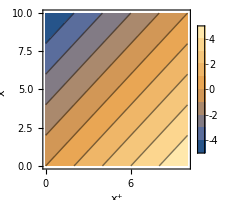

```mathematica
Rotate[
ContourPlot[FNx[xpl,xmn],{xpl,0,10},{xmn,0,10},
ImageSize->200,
FrameLabel->{{"x^-",None},{"x^+",None}},
FrameStyle->Directive[Black,Medium],
PlotRangeClipping->True,
PlotLegends->Automatic
],
 45 Degree]
```

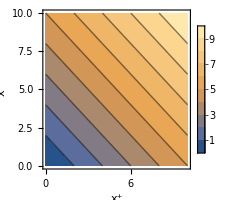

```mathematica
zThis=0;
Rotate[
ContourPlot[FNτ[xpl,xmn,zThis],{xpl,0,10},{xmn,0,10},
FrameLabel->{{"x^-",None},{"x^+",None}},
ImageSize->200,
FrameStyle->Directive[Black,Medium],
PlotRangeClipping->True,
PlotLegends->Automatic
],
 45 Degree]
```

```mathematica
ContourPlot3D[FNτ[xpl,xmn,z],{xpl,0,10},{xmn,0,10},
{z,-10,10},
PlotPoints->10,
AxesLabel->{"x^-","x^+","z"},
PlotLegends->Automatic
]
```

produce field data

```mathematica
coefA=.01;
coefB=.03;
xpl=1;
xmn=1;
y=.1;
z=.2;
fa=1;
ct=.1;
FNAtemp[coefA,coefB,xpl,xmn,y,z,fa,ct]
```

{-6.95587×10^-7,-6.95587×10^-7,-0.00188661,-3.47793×10^-6}

```mathematica
Atempdata=ParallelTable[{xpl,xmn,y,z,FNAtemp[coefA,coefB,xpl,xmn,y,z,fa,ct]//Chop},{xpl,0,10},{xmn,0,10},{y,-10,10},{z,-10,10}];
```

```mathematica
Atempdata//Dimensions
```

{11,11,21,21,5}

single plot

```mathematica
xplmnlist=Table[i,{i,0,10,1}];
yzlist=Table[i,{i,-10,10,1}];
np=10;
tickIn=4;
ticklist=Table[{i,i-np-1},{i,1,np 2+1,tickIn}];

xplInd=10;
xmnInd=2;

xplThis=xplmnlist[[xplInd]];
xmnThis=xplmnlist[[xmnInd]];

data=Atempdata[[xplInd,xmnInd]];

dataf=Flatten[data,1];
dataf//Dimensions

datayzplot=dataf[[All,3;;4]];
datayzplot//Dimensions

dataAmuplot=dataf[[All,5]];
dataAmuplot//Dimensions
```

{441,5}

{441,2}

{441,4}

```mathematica
labelA={"(A^+)_temp","(A^-)_temp","(A^y)_temp","(A^z)_temp"};

figs=Table[
figtitle=labelA[[Aind]]<>"(x^+="<>ToString[xplThis]<>", x^-="<>ToString[xmnThis]<>")";
ll=ArrayReshape[dataAmuplot[[All,Aind]],{21,21}];
fig=MatrixPlot[
ll,
PlotRange->All,
ImageSize->200,
PlotLegends->Automatic,
FrameLabel->{{"z",figtitle},{"y",None}},
FrameStyle->gFrameStyle[fontsizeS],
FrameTicks->{{ticklist,None},{ticklist,None}}
],
{Aind,1,4}
];

Row[figs]
```

-Graphics--Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

compiled figure data

```mathematica
figsxplxmn=Table[

xplThis=xplmnlist[[xplInd]];
xmnThis=xplmnlist[[xmnInd]];

data=Atempdata[[xplInd,xmnInd]];

dataf=Flatten[data,1];

datayzplot=dataf[[All,3;;4]];

dataAmuplot=dataf[[All,5]];

figs=Table[
figtitle=labelA[[Aind]]<>"(x^+="<>ToString[xplThis]<>", x^-="<>ToString[xmnThis]<>")";
ll=ArrayReshape[dataAmuplot[[All,Aind]],{21,21}];
fig=MatrixPlot[
ll,
PlotRange->All,
ImageSize->200,
PlotLegends->Automatic,
FrameLabel->{{"z",figtitle},{"y",None}},
FrameStyle->gFrameStyle[fontsizeS],
FrameTicks->{{ticklist,None},{ticklist,None}}
],
{Aind,1,4}
]
,{xplInd,1,11},{xmnInd,1,11}];
```

Fix x^+

```mathematica
Do[
ll=figsxplxmn[[xplInd,All]];
Row[{ListAnimate[ll[[All,1]]],ListAnimate[ll[[All,2]]],ListAnimate[ll[[All,3]]],ListAnimate[ll[[All,4]]]}]//Print
,{xplInd,1,11,4}]
```

Fix x^-

```mathematica
Do[
ll=figsxplxmn[[All,xmnInd]];
Row[{ListAnimate[ll[[All,1]]],ListAnimate[ll[[All,2]]],ListAnimate[ll[[All,3]]],ListAnimate[ll[[All,4]]]}]//Print
,{xmnInd,1,11,4}]
```

### In the LC gauge

#### Gauge transformation

Unit-step gauge transformation operator; for each x^+,y,z, generate a list of step-size U_LC^† at a series of x^-

```mathematica
FNUALCUnit[Atemppls_,dxmn_]:=
Module[{
m0,
res
},
m0=cltensor[Atemppls];
MatrixExp[ⅈ gg.5 dxmn m0]
];
```

```mathematica
(* Generate A_temp for each coordinate point *)
nperp=10;
nppl=10;
npmn=10;
nperpDim=2 nperp+1;
npplDim=nppl+1;
npmnDim=npmn+1;
perplist=Table[y,{y,-nperp,nperp}];
pllist=Table[m,{m,0,nppl}];

Atempdatas=Table[
ParallelTable[{xpl,xmn,y,z,FNAtemp[coefA,coefB,xpl,xmn,y,z,fa,ct]//Chop},{xpl,0,nppl},{xmn,0,npmn},{y,-nperp,nperp},{z,-nperp,nperp}]
,{fa,1,8}];

Atempdatas//Dimensions
```

{8,11,11,21,21,5}

```mathematica
(* Check a sample *)
Atempdatas[[1;;8,10,11,5,5,5]]
```

{{0.000210796,-0.000154743,0.00219323,-0.0000443755},{0.000362174,-0.000368904,0.00438647,5.3274×10^-6},{0.000528918,-0.000567699,0.0065797,0.0000307016},{0.00069642,-0.000765736,0.00877294,0.0000548748},{0.000904058,-0.000923637,0.0109662,0.0000154997},{0.00108144,-0.00111179,0.0131594,0.0000240299},{0.00128666,-0.00127211,0.0153526,-0.0000115148},{0.0014753,-0.00144902,0.0175459,-0.0000208041}}

```mathematica
(* Test FNUALCUnit *)
xplInd=10;
xmnInd=10;
yInd=5;
zInd=5;
Apls=Atempdatas[[1;;8,xplInd,xmnInd,yInd,zInd,5,1]];
resm=FNUALCUnit[Apls,dxmn];
resm//MatrixForm
resm.ConjugateTranspose[resm]//Chop//MatrixForm
```

(1.-0.0000423394 ⅈ | -0.0000120739+0.000100527 ⅈ | -0.0000351151-0.000124305 ⅈ
0.0000120626+0.000100522 ⅈ | 1.+0.0000967579 ⅈ | 0.0000260917-0.0000544372 ⅈ
0.0000351083-0.000124312 ⅈ | -0.0000260773-0.0000544333 ⅈ | 1.-0.0000544185 ⅈ)

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

```mathematica
dxmn=1;
(* Get unit ULC at each coordinate point *)
UAtempdatasUnit=Table[
Apls=Atempdatas[[1;;8,xplInd,xmnInd,yInd,zInd,5,1]];
FNUALCUnit[Apls,dxmn]
,{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,1,nperpDim}
];
```

Gauge transformation operator; for each x^-, product all unit-step gauge transformation operator of all the previous x^- sequentially

```mathematica
(* Get ULC at each coordinate point *)
UAtempdatas=UAtempdatasUnit;
Do[
UAtempdatas[[xplInd,xmnInd,yInd,zInd]]=
UAtempdatas[[xplInd,xmnInd-1,yInd,zInd]].UAtempdatas[[xplInd,xmnInd,yInd,zInd]]
,{xplInd,1,npplDim},{yInd,1,nperpDim},{zInd,1,nperpDim},{xmnInd,2,npmnDim}
];
```

```mathematica
UAtempdatas//Dimensions
```

{11,11,21,21,3,3}

Take derivative of the gauge transformation operators

single-point derivative, version 1, finite difference method, 1st order

```mathematica
dxpl=1;
dxplInv=1/dxpl;
(* Get A derivate at each coordinate point *)
AplsDmn=Atempdatas[[All,All,All,All,All,5,1]] dxplInv;
Do[
AplsDmn[[fa,xplInd,xmnInd,yInd,zInd]]=
dxplInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd-1,xmnInd,yInd,zInd,5,1]])
,{xplInd,2,11},{xmnInd,1,11},{yInd,1,21},{zInd,1,21},
{fa,1,8}];

dyInv=1;
AplsDy=Atempdatas[[All,All,All,All,All,5,1]]dyInv;
Do[
AplsDy[[fa,xplInd,xmnInd,yInd,zInd]]=
dyInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd,xmnInd,yInd-1,zInd,5,1]]);
,{xplInd,1,11},{xmnInd,1,11},{yInd,2,21},{zInd,1,21},
{fa,1,8}];

dzInv=1;
AplsDz=Atempdatas[[All,All,All,All,All,5,1]] dzInv;
Do[
AplsDz[[fa,xplInd,xmnInd,yInd,zInd]]=
dzInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd,xmnInd,yInd,zInd-1,5,1]]);
,{xplInd,1,11},{xmnInd,1,11},{yInd,1,21},{zInd,2,21},
{fa,1,8}];
```

single-point derivative, version 2, finite difference method, 1st order, periodic boundary condition on y [TAKEN]

```mathematica
(* Get the dimension of A^+ data at all coordinate points *)
tmp=Atempdatas[[All,All,All,All,All,5,1]] ;
datanDim=Dimensions[tmp];
```

```mathematica
dxpl=1;
dxplInv=1/dxpl;
(* Get A derivate at each coordinate point *)
AplsDmn=ConstantArray[0,datanDim];
Do[
AplsDmn[[fa,xplInd,xmnInd,yInd,zInd]]=
dxplInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd-1,xmnInd,yInd,zInd,5,1]])
,{xplInd,2,npplDim},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,1,nperpDim},
{fa,1,8}];
(* Assume the field is 0 before x^+=0 *)
Do[
AplsDmn[[fa,xplInd,xmnInd,yInd,zInd]]=
dxplInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-0)
,{xplInd,1,1},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,1,nperpDim},
{fa,1,8}];

dyInv=1;
AplsDy=ConstantArray[0,datanDim];
Do[
AplsDy[[fa,xplInd,xmnInd,yInd,zInd]]=
dyInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd,xmnInd,yInd-1,zInd,5,1]]);
,{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,2,nperpDim},{zInd,1,nperpDim},
{fa,1,8}];
(* Assume the field is periodical in y *)
Do[
AplsDy[[fa,xplInd,xmnInd,yInd,zInd]]=
dyInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd,xmnInd,nperpDim,zInd,5,1]]);
,{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,1,1},{zInd,1,nperpDim},
{fa,1,8}];

dzInv=1;
AplsDz=ConstantArray[0,datanDim];
Do[
AplsDz[[fa,xplInd,xmnInd,yInd,zInd]]=
dzInv(Atempdatas[[fa,xplInd,xmnInd,yInd,zInd,5,1]]-Atempdatas[[fa,xplInd,xmnInd,yInd,zInd-1,5,1]]);
,{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,2,nperpDim},
{fa,1,8}];
```

Sum the derivative

```mathematica
(* Get summed A derivate at each coordinate point *)
AplsDmnSum=AplsDmn;
Do[
AplsDmnSum[[fa,xplInd,xmnInd,yInd,zInd]]=
AplsDmnSum[[fa,xplInd,xmnInd,yInd,zInd]]+AplsDmnSum[[fa,xplInd,xmnInd-1,yInd,zInd]],
{fa,1,8},{xplInd,1,npplDim},{yInd,1,nperpDim},{zInd,1,nperpDim},
{xmnInd,2,11}];

AplsDySum=AplsDy;
Do[
AplsDySum[[fa,xplInd,xmnInd,yInd,zInd]]=
AplsDySum[[fa,xplInd,xmnInd,yInd,zInd]]+AplsDySum[[fa,xplInd,xmnInd-1,yInd,zInd]],
{fa,1,8},{xplInd,1,npplDim},{yInd,1,nperpDim},{zInd,1,nperpDim},
{xmnInd,2,11}];

AplsDzSum=AplsDz;
Do[
AplsDzSum[[fa,xplInd,xmnInd,yInd,zInd]]=
AplsDzSum[[fa,xplInd,xmnInd,yInd,zInd]]+AplsDzSum[[fa,xplInd,xmnInd-1,yInd,zInd]],
{fa,1,8},{xplInd,1,npplDim},{yInd,1,nperpDim},{zInd,1,nperpDim},
{xmnInd,2,11}];
```

```mathematica
AplsDmnSum//Dimensions
AplsDySum//Dimensions
AplsDzSum//Dimensions
```

{8,11,11,21,21}

{8,11,11,21,21}

{8,11,11,21,21}

Apply gauge transformation operators to the field

-Graphics-

```mathematica
(* Get A^- in LC *)

AbsoluteTiming[
ALCmn=Table[

ULCdagger=UAtempdatas[[xplInd,xmnInd,yInd,zInd]];
ULC=ConjugateTranspose[ULCdagger];

Amn=Atempdatas[[1;;8,xplInd,xmnInd,yInd,zInd,5,2]];
AmnMatrix=cltensor[Amn];

AplDmn=AplsDmnSum[[1;;8,xplInd,xmnInd,yInd,zInd]];
AplDmnMatrix=cltensor[AplDmn];

resm=ULC.(AmnMatrix-dxmn AplDmnMatrix).ULCdagger;
cltensorInv[resm],
{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,1,nperpDim}
];
]
```

{4.79917,Null}

```mathematica
(* Get Ay in LC *)

AbsoluteTiming[
ALCy=Table[

ULCdagger=UAtempdatas[[xplInd,xmnInd,yInd,zInd]];
ULC=ConjugateTranspose[ULCdagger];

Ay=Atempdatas[[1;;8,xplInd,xmnInd,yInd,zInd,5,3]];
AyMatrix=cltensor[Ay];

AplDy=AplsDySum[[1;;8,xplInd,xmnInd,yInd,zInd]];
AplDyMatrix=cltensor[AplDy];

resm=ULC.(AyMatrix+.5dxmn AplDyMatrix).ULCdagger;
cltensorInv[resm],
{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,1,nperpDim}
];
]
```

{4.76813,Null}

```mathematica
(* Get Az in LC *)
SU30=ConstantArray[0,{3,3}];
AbsoluteTiming[
ALCz=Table[
z=perplist[[zInd]];
xpl=pllist[[xplInd]];
xmn=pllist[[xmnInd]];
zref=.5(xpl+xmn);
If[z>zref,
resm=SU30,
ULCdagger=UAtempdatas[[xplInd,xmnInd,yInd,zInd]];
ULC=ConjugateTranspose[ULCdagger];

Az=Atempdatas[[1;;8,xplInd,xmnInd,yInd,zInd,5,4]];
AzMatrix=cltensor[Az];

AplDz=AplsDzSum[[1;;8,xplInd,xmnInd,yInd,zInd]];
AplDzMatrix=cltensor[AplDz];

resm=ULC.(AzMatrix+.5dxmn AplDzMatrix).ULCdagger];
cltensorInv[resm],
{xplInd,1,npplDim},{xmnInd,1,npmnDim},{yInd,1,nperpDim},{zInd,1,nperpDim}
];
]
```

{3.75531,Null}

Plot the field

```mathematica
ALCs={ALCmn,ALCy,ALCz}//Chop;
```

```mathematica
xplmnlist=Table[i,{i,0,10,1}];
yzlist=Table[i,{i,-10,10,1}];
np=10;
tickIn=4;
ticklist=Table[{i,i-np-1},{i,1,np 2+1,tickIn}];

xplInd=10;
xmnInd=2;

xplThis=xplmnlist[[xplInd]];
xmnThis=xplmnlist[[xmnInd]];


colorInd=1;
data1=ALCmn[[xplInd,xmnInd,All,All,colorInd]];
data2=ALCy[[xplInd,xmnInd,All,All,colorInd]];
data3=ALCz[[xplInd,xmnInd,All,All,colorInd]];
datas={data1,data2,data3};
```

```mathematica
labelA={"(A^-)_LC","(A^y)_LC","(A^z)_LC"};

figs=Table[
figtitle=labelA[[Aind]]<>"(x^+="<>ToString[xplThis]<>", x^-="<>ToString[xmnThis]<>")";
ll=datas[[Aind]];
fig=MatrixPlot[
ll,
PlotRange->All,
ImageSize->200,
PlotLegends->Automatic,
FrameLabel->{{"z",figtitle},{"y",None}},
FrameStyle->gFrameStyle[fontsizeS],
FrameTicks->{{ticklist,None},{ticklist,None}}
],
{Aind,1,3}
];

Row[figs]
```

-Graphics--Graphics--Graphics-

Result

-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-